# Script for PN & BoB matching 1:1 Mass ratio

## to accompany https://arxiv.org/abs/2203.08998

Author: Maria Babiuc-Hamilton

```mathematica
ClearAll["Global`*"];Off[General::spell];Remove["Global`*"]
SetOptions[Simplify,TimeConstraint->1000];
$Assumptions=η>0 &&t∈Reals;
Unprotect[Sqrt]; Sqrt[x_^2]:=x; Protect[Sqrt];
$MinPrecision=20; (* $MachinePrecision;*)
```

Now we re-implement the PN

```mathematica
m1 =0.5000000618087954;
m2=1-m1;
M=m1+m2;
μ=(m1*m2)/M;
η=N[μ/M];
γ=0.5772156649;
```

Pick initial data for the inspiral

```mathematica
etLow = 10^-3;
```

```mathematica
r0 = 10;rIS = 6;rLR=4;
Mω0 =N[(r0)^(-3/2)]
MωIS =N[(rIS)^(-3/2)]
MωLR =N[(rLR)^(-3/2)]
Tc0 =Simplify[ 5/256(r0 M)^4/(m1 m2 M)]
```

0.0316228

0.0680414

0.125

781.25

```mathematica
x0=N[Simplify[(Mω0)^(2/3) ]]
xIS=N[Simplify[(MωIS)^(2/3) ]]
xLR=N[Simplify[(MωLR)^(2/3) ]]
```

0.1

0.166667

0.25

```mathematica
xLow=x0;
```

Those are the instantaneous terms for xdot taken from arXiv:1609.05933 (A3-A6)

```mathematica
xdot0PN = (2(37 et[t]^4+292 et[t]^2+96)η)/(15(1-et[t]^2)^(7/2));
xdot1PN= η/(420(1-et[t]^2)^(9/2))(-(8288η-11717)et[t]^6-14(10122η-12217)et[t]^4-120(1330η-731)et[t]^2-16(924η+743));
xdot2PN = η/(45360(1-et[t]^2)^(11/2))((1964256 η^2-3259980η+3523113)et[t]^8+(64828848 η^2-123108426η+83424402)et[t]^6+(16650606060 η^2-207204264η+783768)et[t]^4+(61282032 η^2+15464736η-92846560)et[t]^2+1903104 η^2+(1-et[t]^2)^(1/2)((2646000-1058400η)et[t]^6+(64532160-25812864η)et[t]^2-580608η+1451520)+4514976η-360224);
xdot3PN=η/(598752000(1-et[t]^2)^(13/2))(25 et[t]^10(2699947161-176η(4η(2320640η-2962791)+16870887))+32 et[t]^2(55η(270(7015568(1-et[t]^2)^(1/2)-9657701)η-8125851600(1-et[t]^2)^(1/2)+38745 π^2(1121(1-et[t]^2)^(1/2)+1185)-901169500 η^2+5387647438)+31050413856(1-et[t]^2)^(1/2)+358275866598)+128(-275η(81(16073-17696(1-et[t]^2)^(1/2))η-1066392(1-et[t]^2)^(1/2)+46494 π^2((1-et[t]^2)^(1/2)-45)+470820 η^2+57265081)-3950984268(1-et[t]^2)^(1/2)+12902173599)+et[t]^8(162(1240866000(1-et[t]^2)^(1/2)+19698134267)-1100η(16η(-3582684(1-et[t]^2)^(1/2)+137570300η-286933509)+27(6843728(1-et[t]^2)^(1/2)+255717 π^2+173696120)))+12 et[t]^6(55η(90(52007648(1-et[t]^2)^(1/2)+311841025)η+3(4305 π^2(14(1-et[t]^2)^(1/2)-19113)-5464335200(1-et[t]^2)^(1/2)+767166806)-17925404000 η^2)+742016570592(1-et[t]^2)^(1/2)+6005081022)+8 et[t]^4(55η(270(71069152(1-et[t]^2)^(1/2)+6532945)η-74508169680(1-et[t]^2)^(1/2)+116235 π^2(1510(1-et[t]^2)^(1/2)-4807)-23638717900 η^2+88628306866)+6(332891836596(1-et[t]^2)^(1/2)+8654689873))+40677120(891 et[t]^8+28016 et[t]^6+82736 et[t]^4+43520 et[t]^2+3072)Log[x[t]/xLow*(1+(1-et[t]^2)^(1/2))/(2(1-et[t]^2))]);
```

Those are the instantaneous terms for etdot taken from arXiv:0908.3854v2 (6.19a-6.19d)

```mathematica
etdot0PN=(-et[t](121 et[t]^2+304)η)/(15(1-et[t]^2)^(5/2));
etdot1PN = (et[t]*η)/(2520(1-et[t]^2)^(7/2))((93184η-125361)et[t]^4+12(54271η-59834)et[t]^2+8(28588η+8451));
etdot2PN = (-et[t]*η)/(30240(1-et[t]^2)^(9/2))((2758560 η^2-4344852η+3786543)et[t]^6+(42810096 η^2-78112266η+46579718)et[t]^4+(48711348 η^2-35583228η-36993396)et[t]^2+4548096 η^2+(1-et[t]^2)^(1/2)((2847600-1139040η)et[t]^4+(35093520-14037408η)et[t]^2-5386752η+13466880)+13509360η-15198032);
etdot3PN=(-et[t]η)/((1-et[t]^2)^(11/2))(54177075619/6237000+(7198067/22680+1283/10 π^2)η-3000281/2520 η^2-61001/486 η^3+et[t]^2(6346360709/891000+(9569213/360+54001/960 π^2)η+12478601/15120 η^2-86910509/19440 η^3)+et[t]^4(-126288160777/16632000+(418129451/181440-254903/1920 π^2)η+478808759/20160 η^2-2223241/180 η^3)+et[t]^6(5845342193/1232000+(-98425673/10080-6519/640 π^2)η+6538757/630 η^2-11792069/2430 η^3)+et[t]^8(302322169/1774080-1921387/10080 η+41179/216 η^2-193396/1215 η^3)+(1-et[t]^2)^(1/2)(-22713049/15750+(-5526991/945+8323/180 π^2)η+54332/45 η^2+et[t]^2(89395687/7875+(-38295557/1260+94177/960 π^2)η+681989/90 η^2)+et[t]^4(5321445613/378000+(-26478311/1512+2501/2880 π^2)η+225106/45 η^2)+et[t]^6(186961/336-289691/504 η+3197/18 η^2))+730168/23625*1/(1+(1-et[t]^2)^(1/2))+304/15(82283/1995+297674/1995 et[t]^2+1147147/15960 et[t]^4+61311/21280 et[t]^6)Log[x[t]/xLow*(1+(1-et[t]^2)^(1/2))/(2(1-et[t]^2))]);
```

The more accurate calculation of the functions entering in the hereditary terms up to eccentricity 0.7 are: arXiv:1609.05933 ϕe (A11), tϕe (A12), φe(A10)

```mathematica
ε=(1.-et[t]^2)^(-1/2);
aϕe = ε^10(1.+18970894028/2649026657 et[t]^2+157473274/30734301 et[t]^4+48176523/177473701 et[t]^6+9293260/3542508891 et[t]^8-5034498/7491716851 et[t]^10+ 428340/9958749469 et[t]^12);
atϕe = ε^7(1.+413137256/136292703 et[t]^2+37570495/98143337 et[t]^4-2640201/993226448 et[t]^6-4679700/6316712563 et[t]^8-328675/8674876481 et[t]^10);
aφee=192/985((1-et[t]^2)^(1/2))/et[t]^2((1-et[t]^2)^(1/2)aϕe -atϕe);
```

More functions entering in the hereditary terms: arXiv:1609.05933 ψe(A13), ζe(A14), κe(A15)

```mathematica
aψe=ε^12(1.- 185/21 et[t]^2-3733/99 et[t]^4-1423/104 et[t]^6);
aζe=ε^12(1.+ 2095/143 et[t]^2+1590/59 et[t]^4+977/113 et[t]^6);
aκe=ε^14(1.+ 1497/79 et[t]^2+7021/143 et[t]^4+997/98 et[t]^6+463/51 et[t]^8-3829/120 et[t]^10);
```

And their tilde: arXiv:1609.05933 tψe(A16), tζe(A17), tκe(A18)

```mathematica
atψe=ε^9(1- 2022/305 et[t]^2-249/26 et[t]^4-193/239 et[t]^6+23/43 et[t]^8-102/463 et[t]^10);
atζe=ε^9(1+ 1563/194 et[t]^2+1142/193 et[t]^4+123/281 et[t]^6-27/328 et[t]^8);
atκe=ε^10(1+ 1789/167 et[t]^2+5391/340 et[t]^4+2150/219 et[t]^6-1007/320 et[t]^8+2588/189 et[t]^10);
```

And now, from arXiv:0908.3854, we take Fe (6.9),  ψne(6.22a), ζne(6.22b)

```mathematica
aFe=ε^13(1+85/6 et[t]^2+5171/192 et[t]^4+1751/192 et[t]^6+297/1024 et[t]^8);
aψne=1344/17599 (7-5 et[t]^2)/(1-et[t]^2) aϕe  + 8191/17599 aψe;
aζne=583/567 aζe-16/567 aϕe ;
```

And last, from arXiv:0908.3854, follows φee is the same (see 6.22h), ψee(6.22i), ζee(6.22j), kee(6.22k) and lastly Fee(6.23)

```mathematica
aψee=18816/55691 1/(et[t]^2(1-et[t]^2)^(1/2)) ((1-et[t]^2)^(1/2)(1-11/7 et[t]^2)aϕe -(1-3/7 et[t]^2)atϕe )+16382/55691 ((1-et[t]^2)^(1/2))/et[t]^2((1-et[t]^2)^(1/2)aψe-atψe);
aζee=924/19067 1/(et[t]^2(1-et[t]^2)^(1/2)) (-(1-et[t]^2)^(3/2)aϕe +(1-5/11 et[t]^2)atϕe)+12243/76268 ((1-et[t]^2)^(1/2))/et[t]^2((1-et[t]^2)^(1/2)aζe-atζe);
aκee=((1-et[t]^2)^(1/2))/et[t]^2((1-et[t]^2)^(1/2)aκe-atκe)(769/96-3059665/700566 Log[2.] +8190315/1868176 Log[3.])^-1;
aFee=ε^11(1+2782/769 et[t]^2+10721/6152 et[t]^4+1719/24608 et[t]^6);
```

Those are the hereditary terms for xdot taken from arXiv:1609.05933 (A7)

```mathematica
xdotHT = η x[t]^(13/2)((256 π)/5 aϕe+((256 π)/(1-et[t]^2)aϕe+2/3(-(17599 π)/35 aψne -(2268 η π)/5 aζne -(788 π et[t]^2)/(1-et[t]^2)aφee))x[t] +64/18375(-116761 aκe +(19600 π^2 - 59920 γ-59920 Log[(4 x[t]^(3/2))/xLow])aFe)x[t]^(3/2));
```

Those are the hereditary terms for etdot  taken from arXiv:1609.05933 (A20)

```mathematica
etdotHT =  32/5 et[t]η x[t]^4(-985/48 π x[t]^(3/2)aφee+π x[t]^(5/2) (55691/1344 aψee + 19067/126 η aζee) + x[t]^3((89789209/352800-87419/630 Log[2.]+78003/560 Log[3.]) aκee -769/96(16/3 π^2 -1712/105 γ-1712/105 Log[(4 x[t]^(3/2))/xLow] )aFee));
```

Adding the 6PN Quasi-circular corrections

```mathematica
xdot3p5PNQC=(64π)/5*η*x[t]^5*(-4415/4032+358675/6048 η+91945/1512 η^2)x[t]^(7/2);
α0=153.8803;
α1=-55.13;
α2=588;
α3=-1144;
a4=-5η*α0-(97 η^4)/3888-(18929389 η^3)/435456-(3157 π^2*η^2)/144+(54732199 η^2)/93312-47468/315*η*Log[x[t]]-(31495 π^2*η)/8064-(856γ*η)/315+(59292668653η)/838252800-1712/315 η*Log[2]+(124741Log[x[t]])/8820-(361 π^2)/126+(124741γ)/4410+3959271176713/25427001600-(47385Log[3])/1568+(127751Log[2])/1470;
a4p5=(9731π*η^3)/1344+(42680611π*η^2)/145152+(205 π^3 η)/6-(51438847π*η)/48384-3424/105 π*Log[x[t]]-(6848γ*π)/105+(343801320119π)/745113600-13696/105 π*Log[2];
a5=(155α0*η^2)/12+(1195α0*η)/336-6η*α1-(11567 η^5)/62208+(51474823 η^4)/1741824+(9799 π^2*η^3)/384-(9007776763 η^3)/11757312+216619/189 η^2*Log[x[t]]-(126809 π^2*η^2)/3024-(2354γ*η^2)/945+(1362630004933 η^2)/914457600-4708/945 η^2*Log[2]+(53963197η*Log[x[t]])/52920+(14555455 π^2*η)/217728+(3090781γ*η)/26460-(847101477593593η)/228843014400-(15795η*Log[3])/3136+(2105111η*Log[2])/8820-(5910592*Log[x[t]])/1964655-(21512 π^2)/1701-(11821184γ)/1964655+29619150939541789/36248733480960+(616005Log[3])/3136-(107638990Log[2])/392931;
a5p5=-20*π*η*α0+(49187π*η^4)/6048-(7030123π*η^3)/13608-(112955 π^3*η^2)/576+(1760705531π*η^2)/290304-189872/315 π*η*Log[x[t]]-(26035 π^3*η)/16128-(3424γ*π*η)/315-(2437749208561π*η)/4470681600-6848/315 π*η*Log[2]+(311233π*Log[x[t]])/11760+(311233γ*π)/5880+(91347297344213π)/81366405120-142155/784 π*Log[3]+(5069891π*Log[2])/17640;
a6=-(535α0*η^3)/36+(7295α0*η^2)/336-(248065α0*η)/4536+(31α1*η^2)/2+(239α1*η)/56-7α2*η-7α3*η*Log[x[t]]-α3*η-(155377 η^6)/1679616-(152154269 η^5)/10450944-(1039145 π^2*η^4)/62208+(76527233921 η^4)/94058496-(41026693 η^3*Log[x[t]])/17010+(55082725 π^2*η^3)/217728-(2033γ*η^3)/1701-(56909847373567 η^3)/7242504192-(4066 η^3*Log[2])/1701-(271237829 η^2*Log[x[t]])/127008+(92455 π^4*η^2)/1152-(4061971769 π^2*η^2)/870912-(21169753γ*η^2)/317520+(3840832667727673 η^2)/55477094400-(57915 η^2*Log[3])/12544-(2724535 η^2*Log[2])/21168-4387/63 π^2*η*Log[x[t]]-(12030840839η*Log[x[t]])/37721376+(410 π^4*η)/9-8774/63 γ*π^2*η+(206470485307 π^2*η)/1005903360+(362623282541γ*η)/94303440-(12413297162366594971η)/271865501107200+(3016845η*Log[3])/12544-17548/63 π^2*η*Log[2]+(701463800861η*Log[2])/94303440+(366368 Log[x[t]]^2)/11025+(2930944Log[2]Log[x[t]])/11025-13696/315 π^2*Log[x[t]]+(1465472γ*Log[x[t]])/11025-(155359670313691Log[x[t]])/157329572400-(27392*N[Zeta[3],25])/105-(256 π^4)/45-(27392γ*π^2)/315+(1414520047 π^2)/2619540+(1465472 γ^2)/11025-(155359670313691γ)/78664786200+1867705968412371074441833/154211174411374080000+(5861888 Log[2]^2)/11025-(37744140625Log[5])/260941824-(63722699919Log[3])/112752640-54784/315 π^2*Log[2]+(5861888γ*Log[2])/11025-(206962178724547Log[2])/78664786200;
xdot4to6PNQC=(64η*x[t]^5)/5(a4*x[t]^4+a4p5*x[t]^(9/2)+a5*x[t]^5+a5p5*x[t]^(11/2)+a6*x[t]^6);
```

Now for the High Accuracy Hereditary Corrections and Instantaneous terms

```mathematica
xdotINSTHT=1/M(xdot0PN*x[t]^5+xdot1PN*x[t]^6+xdot2PN*x[t]^7+xdot3PN*x[t]^8+xdotHT+xdot3p5PNQC
+xdot4to6PNQC);
etdotINSTHT = 1/M(etdot0PN*x[t]^4+etdot1PN*x[t]^5+etdot2PN*x[t]^6+etdot3PN*x[t]^7+etdotHT);
```

#### Time to solve numerically the coupled (e,x) equations

```mathematica
solxet3PNINSTHT=NDSolve[{x'[t]==xdotINSTHT,et'[t]==etdotINSTHT,x[0]==xLow,et[0]==etLow},{x[t],et[t]},{t,0,Infinity}, Method->{"StiffnessSwitching"},AccuracyGoal->Automatic, WorkingPrecision->$MinPrecision, PrecisionGoal->$MinPrecision]; 
x3PN[t_]:=Evaluate[x[t]/.solxet3PNINSTHT]
et3PN[t_]:=Evaluate[et[t]/.solxet3PNINSTHT]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1. ((0.0333333 (96+Times[«2»]+Times[«2»]) x[«1»]^5)/Plus[«2»]^(7/2)+«5»+3.2 x[«1»]^5 (Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»])),et'[t]==1. («1»),x[0]==0.1,et[0]==1/1000},{},{},{},{}}) is less than WorkingPrecision (20.).

NDSolve::ndsz: At t == 531.20526206735869836, step size is effectively zero; singularity or stiff system suspected.

we define  tISCO = tStiff - 20M, for a0 = 4M, from where the eq. becomes stiff. Will need to replace tStiff for different parameters

```mathematica
tStiff=530;
tfinins=tStiff;
```

```mathematica
xLR
x3PNfin=ScientificForm[x3PN[tfinins]]
```

0.25

{2.6205000684789889294×10^-1}

```mathematica
ScientificForm[et3PN[tfinins]]
```

{1.7053702432377584953×10^-4}

```mathematica
Solve[2.62050006847898893 10^-1==(Mωfin)^(2/3),Mωfin]
```

{{Mωfin→0.1341455477303098864}}

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

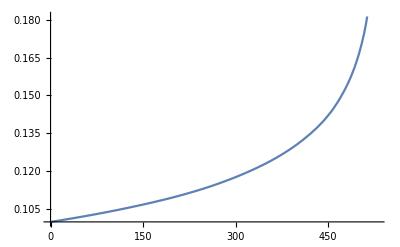

```mathematica
Plot[x3PN[t],{t,0,tfinins}]
```

#### We now work towards finding the eccentric anomaly u.

We need to find the mean anomaly l since we use it to determine the eccentric anomaly.
We use the relation between the mean motion n and the mean anomaly.
The PN corrections for the mean motion are as follows.

```mathematica
n1PN = 3/(et3PN[t]^2-1);
n2PN = ((26η-51)et3PN[t]^2+28η-18)/(4(et3PN[t]^2-1)^2);
n3PN = -1/(128(1-et3PN[t]^2)^(7/2))((1536η-3840)et3PN[t]^4+(1920-768η)et3PN[t]^2-768η+(1-et3PN[t]^2)^(1/2)((1040 η^2-1760η+2496)et3PN[t]^4+(5120 η^2+123 π^2 η-17856η+8544)et3PN[t]^2+896 η^2-14624η+492 η π^2-192)+1920);
ldot = 1/M(x3PN[t]^(3/2)+n1PN*x3PN[t]^(5/2)+n2PN*x3PN[t]^(7/2)+n3PN*x3PN[t]^(9/2));
```

We solve the differential and obtain the equation for the mean anomaly.

```mathematica
soll3PN=NDSolve[{l3PN'[t]- ldot ==0,l3PN[0]==π},l3PN[t],{t,0,tfinins}, Method->{"StiffnessSwitching"},AccuracyGoal->Automatic, WorkingPrecision->$MinPrecision, PrecisionGoal->$MinPrecision];
l[t_]:=Evaluate[l3PN[t]/.soll3PN]
```

NDSolve::precw: The precision of the differential equation ({{{-1. (Power[«2»]+Times[«3»]+Times[«4»]+Times[«4»])+l3PN'[t]}==0,l3PN[0]==π},{},{},{},{}}) is less than WorkingPrecision (20.).

We now use ADM coordinates to code the terms contained in the equation for eccentric anomaly

```mathematica
βt[t_]:=(1-(1-et3PN[t]^2)^(1/2))/et3PN[t];
αADM3PN[t_]:=βt[t]^j(x3PN[t]^2((15-6η)/(j(1-et3PN[t]^2)^(1/2))-(4η+η^2)/4)+x3PN[t]^3((2880(1+et3PN[t]^2)-(10880+2784 et3PN[t]^2-123 π^2)η+(960+1056 et3PN[t]^2)η^2)/(96j(1-et3PN[t]^2)^(3/2))+(7488-(7544-48 et3PN[t]^2-3 π^2)η+(1168+32 et3PN[t]^2)η^2-52(1-et3PN[t]^2)η^3)/(96(1-et3PN[t]^2))+j*(-18η+24 η^2+3 η^3)/(16(1-et3PN[t]^2)^(1/2))+j^2*(13 η^3)/48));
```

The the Bessel functions that are used for the eccentric anomaly, and the anomaly truncated to 10.

```mathematica
AsADM[t_]:= 2/s BesselJ[s,s*et3PN[t]]+Sum[αADM3PN[t](BesselJ[j+s,s*et3PN[t]]-BesselJ[s-j,s*et3PN[t]]),{j,1,10}];
u3PNADM[t_]:= l[t]+Sum[AsADM[t]*Sin[s*l[t]],{s,1,10}];
```

We will interpolate the function to speed up the calculation

```mathematica
u3PNADMinterp=FunctionInterpolation[u3PNADM[t],{t,0,tfinins},InterpolationOrder->10]
```

InterpolatingFunction[…]

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

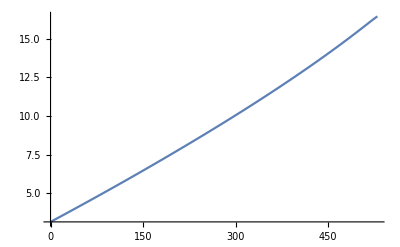

```mathematica
Plot[{u3PNADM[t],u3PNADMinterp},{t,0,tfinins}]
```

Now we need to determine how the distance between the bodies evolves

```mathematica
r0PN[t_]:=1-et3PN[t]*Cos[u3PNADMinterp[t]];
r1PN[t_]:=(2(et3PN[t]*Cos[u3PNADMinterp[t]]-1))/(et3PN[t]^2-1)+1/6(2(η-9)+et3PN[t](7η-6)Cos[u3PNADMinterp[t]]);
r2PN[t_]:=1/((1-et3PN[t]^2)^2)(1/72(8 η^2+30η+72)et3PN[t]^4+1/72(-16 η^2-876η+756)et3PN[t]^2+1/72(8 η^2+198η+360)+(1/72(-35 η^2+231η-72)et3PN[t]^5+1/72(70 η^2-150η-468)et3PN[t]^3+1/72(-35 η^2+567η-648)et3PN[t])Cos[u3PNADMinterp[t]]+(1-et3PN[t]^2)^(1/2)(1/72(360-144η)et3PN[t]^2+1/72(144η-360)+(1/72(180-72η)et3PN[t]^3+1/72(72η-180)et3PN[t])Cos[u3PNADMinterp[t]]));
r3PN[t_]:=1/(181440(1-et3PN[t]^2)^(7/2))((-665280 η^2+1753920η-1814400)et3PN[t]^6+(725760 η^2-77490 π^2 η+5523840η-3628800)et3PN[t]^4+(544320 η^2+154980 π^2 η-14132160η+7257600)et3PN[t]^2-604800 η^2+6854400η+((302400 η^2-1254960η+453600)et3PN[t]^7+(-1542240 η^2-38745 π^2 η+6980400η-453600)et3PN[t]^5+(2177280 η^2+77490 π^2 η-12373200η+4989600)et3PN[t]^3+(-937440 η^2-38745 π^2 η+6647760η-4989600)et3PN[t])Cos[u3PNADMinterp[t]]+(1-et3PN[t]^2)^(1/2)((-4480 η^3-25200 η^2+22680η-120960)et3PN[t]^6+(13440 η^3+4404960 η^2+116235 π^2 η-12718296η+5261760)et3PN[t]^4+(-13440 η^3+2242800 η^2+348705 π^2 η-19225080η+16148160)et3PN[t]^2+4480 η^3+45360 η^2-8600904η+((-6860 η^3+550620 η^2-986580η+120960)et3PN[t]^7+(20580 η^3-2458260 η^2+3458700η-2358720)et3PN[t]^5+(-20580 η^3-3539340 η^2-116235 π^2 η+20173860η-16148160)et3PN[t]^3+(6860 η^3-1220940 η^2-464940 π^2 η+17875620η-4717440)et3PN[t])Cos[u3PNADMinterp[t]]+116235 π^2 η+1814400)-77490 π^2 η-1814400);
r[t_]:=Simplify[M*(r0PN[t]*x3PN[t]^-1+r1PN[t]+r2PN[t]*x3PN[t]+r3PN[t]*x3PN[t]^2)];
```

```mathematica
rinterp=FunctionInterpolation[r[t],{t,0,tfinins},InterpolationOrder->10]
```

InterpolatingFunction[…]

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

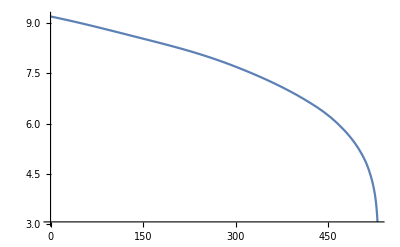

```mathematica
Plot[{r[t],rinterp},{t,0,tfinins}]
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

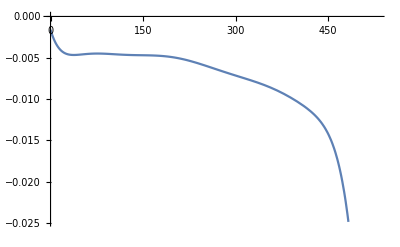

```mathematica
Plot[rinterp'[t],{t,0,tfinins}]
```

Solving for the phase

```mathematica
phid0PN[t_]:=((1-et3PN[t]^2)^(1/2))/(et3PN[t]*Cos[u3PNADMinterp[t]]-1)^2;
phid1PN[t_]:=-((et3PN[t](η-4)(et3PN[t]-Cos[u3PNADMinterp[t]]))/((1-et3PN[t]^2)^(1/2)(et3PN[t]*Cos[u3PNADMinterp[t]]-1)^3));
phid2PN[t_]:=(1/(12(1-et3PN[t]^2)^(3/2)(et3PN[t]*Cos[u3PNADMinterp[t]]-1)^5))((-12 η^2-18η)et3PN[t]^6+(20 η^2-26η-60)et3PN[t]^4+(-2 η^2+50η+75)et3PN[t]^2+((-14 η^2+8η-147)et3PN[t]^5+(8 η^2+22η+42)et3PN[t]^3)*Cos[u3PNADMinterp[t]]^3+((17 η^2-17η+48)et3PN[t]^6+(-4 η^2-38η+153)et3PN[t]^4+(5 η^2-35η+114)et3PN[t]^2)*Cos[u3PNADMinterp[t]]^2-36η+((-η^2+97η+12)et3PN[t]^5+(-16 η^2-74η-81)et3PN[t]^3+(-η^2+67η-246)et3PN[t])*Cos[u3PNADMinterp[t]]+(1-et3PN[t]^2)^(1/2)(et3PN[t]^3(36η-90)*Cos[u3PNADMinterp[t]]^3+((180-72η)et3PN[t]^4+(90-36η)et3PN[t]^2)*Cos[u3PNADMinterp[t]]^2+((144η-360)et3PN[t]^3+(90-36η)et3PN[t])*Cos[u3PNADMinterp[t]]+et3PN[t]^2(180-72η)+36η-90)+90);
phid3PN[t_]:=(1/(13440(1-et3PN[t]^2)^(5/2)(et3PN[t]*Cos[u3PNADMinterp[t]]-1)^7))((10080 η^3+40320 η^2-15120η)et3PN[t]^10+(-52640 η^3-13440 η^2+483280η)et3PN[t]^8+(84000 η^3-190400 η^2-17220 π^2 η-50048η-241920)et3PN[t]^6+(-52640 η^3+516880 η^2+68880 π^2 η-1916048η+262080)et3PN[t]^4+(4480 η^3-412160 η^2-30135 π^2 η+553008η+342720)et3PN[t]^2+((13440 η^3+94640 η^2-113680η-221760)et3PN[t]^9+(-11200 η^3-112000 η^2+12915 π^2 η+692928η-194880)et3PN[t]^7+(4480 η^3+8960 η^2-43050 π^2 η+1127280η-147840)et3PN[t]^5)*Cos[u3PNADMinterp[t]]^5+((-16240 η^3+12880 η^2+18480η)et3PN[t]^10+(16240 η^3-91840 η^2+17220 π^2 η-652192η+100800)et3PN[t]^8+(-55440 η^3+34160 η^2-30135 π^2 η-2185040η+2493120)et3PN[t]^6+(21840 η^3+86800 η^2+163590 π^2 η-5713888η+228480)et3PN[t]^4)Cos[u3PNADMinterp[t]]^4+((560 η^3-137200 η^2+388640η+241920)et3PN[t]^9+(30800 η^3-264880 η^2-68880 π^2 η+624128η+766080)et3PN[t]^7+(66640 η^3+612080 η^2-8610 π^2 η+6666080η-6652800)et3PN[t]^5+(-30800 η^3-294000 η^2-223860 π^2 η+9386432η)et3PN[t]^3)Cos[u3PNADMinterp[t]]^3+67200 η^2+((4480 η^3-20160 η^2+16800η)et3PN[t]^10+(3920 η^3+475440 η^2-17220 π^2 η+831952η-725760)et3PN[t]^8+(-75600 η^3+96880 η^2+154980 π^2 η-3249488η-685440)et3PN[t]^6+(5040 η^3-659120 η^2+25830 π^2 η-7356624η+6948480)et3PN[t]^4+(-5040 η^3+190960 η^2+137760 π^2 η-7307920η+107520)et3PN[t]^2)Cos[u3PNADMinterp[t]]^2-761600η+((-2240 η^3-168000 η^2-424480η)et3PN[t]^9+(28560 η^3+242480 η^2+34440 π^2 η-1340224η+725760)et3PN[t]^7+(-33040 η^3-754880 η^2-172200 π^2 η+5458480η-221760)et3PN[t]^5+(40880 η^3+738640 η^2+30135 π^2 η+1554048η-2936640)et3PN[t]^3+(-560 η^3-100240 η^2-43050 π^2 η+3284816η-389760)et3PN[t])Cos[u3PNADMinterp[t]]+(1-et3PN[t]^2)^(1/2)(((-127680 η^2+544320η-739200)et3PN[t]^7+(-53760 η^2-8610 π^2 η+674240η-67200)et3PN[t]^5)Cos[u3PNADMinterp[t]]^5+((161280 η^2-477120η+537600)et3PN[t]^8+(477120 η^2+17220 π^2 η-2894080η+2217600)et3PN[t]^6+(268800 η^2+25830 π^2 η-2721600η+1276800)et3PN[t]^4)Cos[u3PNADMinterp[t]]^4+((-524160 η^2+1122240η-940800)et3PN[t]^7+(-873600 η^2-68880 π^2 η+7705600η-3897600)et3PN[t]^5+(-416640 η^2-17220 π^2 η+3357760η-3225600)et3PN[t]^3)Cos[u3PNADMinterp[t]]^3+((604800 η^2-504000η-403200)et3PN[t]^6+(1034880 η^2+103320 π^2 η-11195520η+5779200)et3PN[t]^4+(174720 η^2-17220 π^2 η-486080η+2688000)et3PN[t]^2)Cos[u3PNADMinterp[t]]^2+((-282240 η^2-450240η+1478400)et3PN[t]^5+(-719040 η^2-68880 π^2 η+8128960η-5040000)et3PN[t]^3+(94080 η^2+25830 π^2 η-1585920η-470400)et3PN[t])Cos[u3PNADMinterp[t]]-67200 η^2+761600η+et3PN[t]^4(40320 η^2+309120η-672000)+et3PN[t]^2(208320 η^2+17220 π^2 η-2289280η+1680000)-8610 π^2 η-201600)+8610 π^2 η+201600)
phidot[t_]:=1/M(phid0PN[t]*x3PN[t]^(3/2)+phid1PN[t]*x3PN[t]^(5/2)+phid2PN[t]*x3PN[t]^(7/2)+phid3PN[t]*x3PN[t]^(9/2));
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

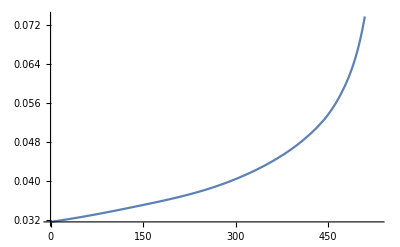

```mathematica
Plot[phidot[t],{t,0,tfinins}]
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

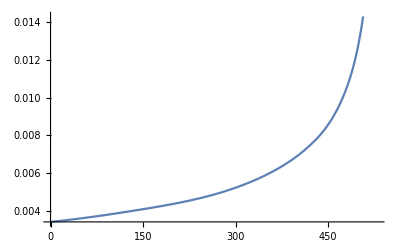

```mathematica
Plot[phidot[t]/r[t],{t,0,tfinins}]
```

We solve for the phase:

```mathematica
solphi3PN=NDSolve[{phiADM'[t]- phidot[t]==0,phiADM[0]==0},phiADM[t],{t,0,tfinins},Method->{"StiffnessSwitching"},AccuracyGoal->Automatic, WorkingPrecision->$MinPrecision, PrecisionGoal->$MinPrecision];
```

NDSolve::precw: The precision of the differential equation ({{{-1. (Times[«3»]+Times[«6»]+Times[«5»]+Times[«5»])+phiADM'[t]}==0,phiADM[0]==0},{},{},{},{}}) is less than WorkingPrecision (20.).

```mathematica
phi[t_]:=Evaluate[phiADM[t]/.solphi3PN]
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

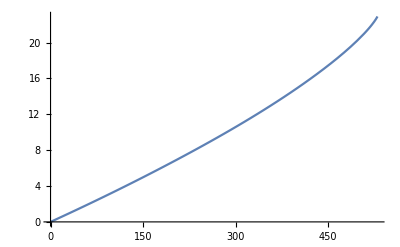

```mathematica
Plot[phi[t],{t,0,tfinins}]
```

```mathematica
phidot[tfinins]
```

{0.13407}

#### The Strain

```mathematica
hre[t_]:=-2M η((-rinterp'[t]^2+r[t]^2 phidot[t]^2+M r[t]^-1)Cos[2*phi[t]] +2*r[t]*rinterp'[t]*phidot[t]Sin[2*phi[t]]);
him[t_]:=-2M η((-rinterp'[t]^2+r[t]^2 phidot[t]^2+M r[t]^-1)Sin[2*phi[t]] -2*r[t]*rinterp'[t]*phidot[t]Cos[2*phi[t]]);
hins[t_]:=hre[t]-ⅈ*him[t];
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

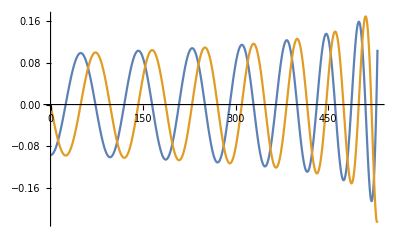

```mathematica
Plot[{hre[t],him[t]},{t,0,tfinins}]
```

Implement the cost function????:

Initial and final parameters

From FinalSpinMassQNM.nb,  values for equal non-spinning binaries χf0Meq and Mfχ0Meq

```mathematica
χf=0.686526691452522(*nonspinning individual BSs in the binary *)
```

0.686527

```mathematica
Mf=0.95158896875;
```

We take the mean value for equal non-spinning binaries from FinalSpinMassQNM.nb,  for l=2, m=2 mode:

```mathematica
MfωQNM = 0.5422370151014632;
QQNM=3.300909722911351;
ωQNM=MfωQNM/Mf
τ = 2 QQNM/ωQNM
```

0.569823

11.5857

Freely chosen parameters

```mathematica
Ap=1;R=1;tp=0;
```

Starting BOB formulation

```mathematica
Ωisco=(-0.091933*χf+0.097593)/(χf^2-2.4228*χf+1.4366)
ωqnm=1.5251-1.1568*(1-χf)^0.1292
```

0.140958

0.529311

take the initial values from the inspiral for ti = tLR

Values taken directly from above.

```mathematica
phidot[tfinins]
phidot'[tfinins]
```

{0.13407}

{0.0209927}

```mathematica
Ωfin = 0.13407012845224703 ;
Ωfindot = 0.020992653676238014;
```

```mathematica
phidot[tfinins-20]
phidot'[tfinins-20]
```

{0.0740845}

{0.000795071}

```mathematica
ΩLR = 0.07408453065081907;
ΩLRdot = 0.0007950705436979995;
```

Now we can implement the BoB

```mathematica
Ωi = ΩLR(*Ωisco*) ;
Ωidot = ΩLRdot;
tp =0;
ΩQNM=ωQNM/2;
ti=tp-τ/2 Log[(ΩQNM^4-Ωi^4)/(2*τ*Ωi^3 Ωidot)-1]
```

-39.2396

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

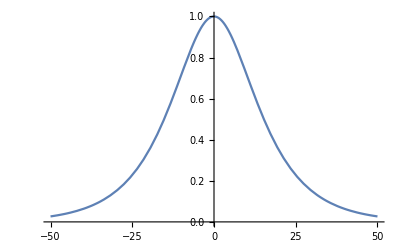

```mathematica
Ap=1;(*1.068*(1-Mf)^0.8918;*)
ψ4[t_]:=Ap*Sech[(t-tp)/τ];
Plot[ψ4[t],{t,-50,50}]
```

```mathematica
kB=((ΩQNM^4-Ωi^4)/(1-Tanh[(ti-tp)/τ]))
```

0.00328334

```mathematica
ΩB[t_]:=(Ωi^4+kB(Tanh[(t-tp)/τ]-Tanh[(ti-tp)/τ]))^(1/4)
```

```mathematica
ωBoB[t_]:=2*ΩB[t];
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

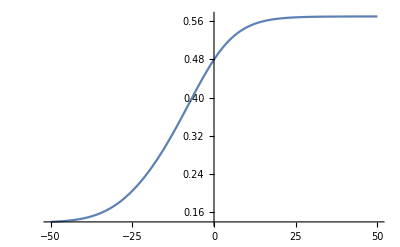

```mathematica
Plot[ωBoB[t],{t,-50,50}]
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

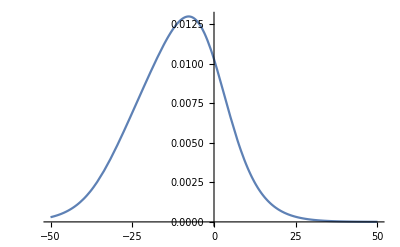

```mathematica
Plot[ωBoB'[t],{t,-50,50}]
```

```mathematica
Kappap=(Ωi^4+kB(1-Tanh[(ti-tp)/τ]))^(1/4)
```

0.284911

```mathematica
Kappam=(Ωi^4-kB(1+Tanh[(ti-tp)/τ]))^(1/4)
```

0.0689673

```mathematica
arctanp[t_]:=Kappap*τ*(ArcTan[(ΩB[t]/Kappap)]-ArcTan[Ωi/Kappap])
arctanm[t_]:=Kappam*τ*(ArcTan[ΩB[t]/Kappam]-ArcTan[Ωi/Kappam])
arctanhp[t_]:=Kappap*τ*(ArcTanh[ΩB[t]/Kappap]-ArcTanh[Ωi/Kappap])
arctanhm[t_]:=Kappam*τ*(ArcTanh[ΩB[t]/Kappam]-ArcTanh[Ωi/Kappam])
```

```mathematica
PhaseB[t_]:=arctanp[t]+arctanhp[t]-arctanm[t]-arctanhm[t]
```

```mathematica
ϕBoB[t_]:=2*PhaseB[t]
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

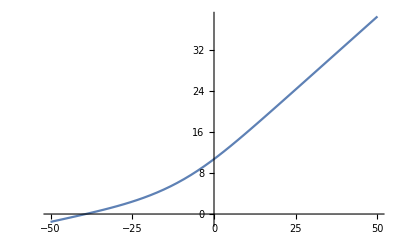

```mathematica
Plot[ϕBoB[t],{t,-50,50}]
```

```mathematica
AmpBoB[t_]:=ψ4[t]/ωBoB[t]^2
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

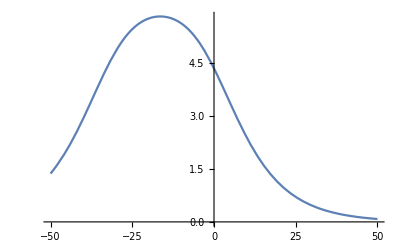

```mathematica
Plot[AmpBoB[t],{t,-50,50}]
```

```mathematica
hBoB[t_]:=AmpBoB[t]*Exp[-ⅈ* ϕBoB[t]]
```

```mathematica
FindMaximum[AmpBoB[t],t]
```

{5.81862,{t→-16.4349}}

```mathematica
t0BoB=-16.30656956691866;
```

```mathematica
MaxAmpBoB=MaxValue[AmpBoB[t],t]
```

5.81862

```mathematica
FindRoot[AmpBoB'[t]==0,{t,-40,40}]
```

{t→-16.4349}

Note that the maximum in amplitude and maximum in the rate of variation of the frequency is not the same!

```mathematica
FindRoot[ωBoB''[t]==0,{t,-40,0}]
```

{t→-7.75385}

```mathematica
tfBoB=-7.742219427214392;
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

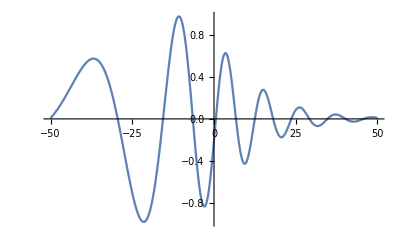

```mathematica
Plot[Re[hBoB[t]]/MaxAmpBoB,{t,-50,50}]
```

```mathematica
NormRehBoB[t_]:=Rescale[Re[hBoB[t]]/MaxAmpBoB,{0,1}];
```

```mathematica
FindMinimum[{NormRehBoB[t],-40<=t<=0},{t,-20}]
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

{-0.978632,{t→-21.5068}}

```mathematica
FindMaximum[{NormRehBoB[t],-40<=t<=0},{t,-10}]
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

{0.9733,{t→-10.7384}}

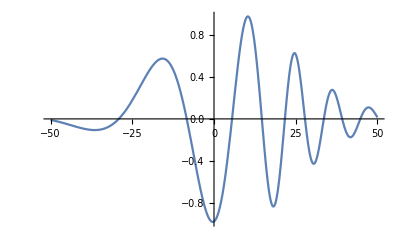

```mathematica
Plot[{NormRehBoB[t-21.109547737391186]},{t,-50,50}]
```

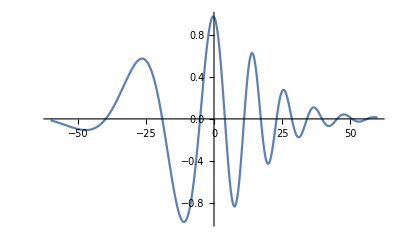

```mathematica
Plot[{NormRehBoB[t-10.475364941329538]},{t,-60,60}]
```

```mathematica
tfinins
```

530

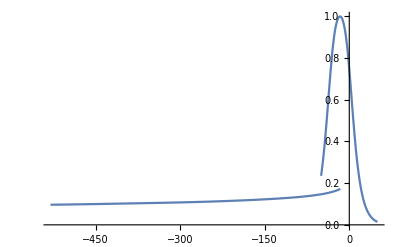

```mathematica
Show[Plot[AmpBoB[t]/MaxAmpBoB,{t,-50,50}],Plot[Abs[hins[t+tfinins]],{t,-tfinins,0}],PlotRange->{{-tfinins,50},All}]
```

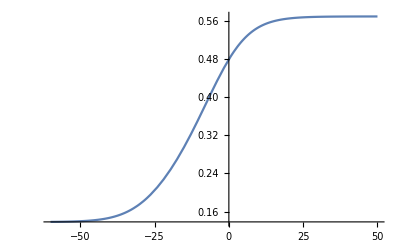

```mathematica
Show[Plot[ϕBoB'[t],{t,-60,50}]]
```

```mathematica
ϕBoB'[0]
```

0.479573

```mathematica
ϕBoB'[-39.2395746350511]
```

0.148169

```mathematica
ωBoB[ti]
```

0.148169

```mathematica
2 phidot[510]
```

{0.148169}

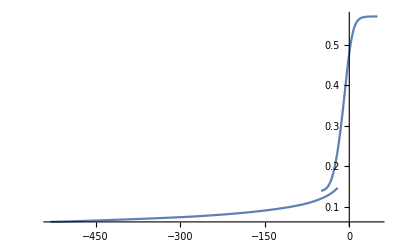

```mathematica
Show[Plot[2 phidot[t+tfinins],{t,-tfinins,0}],Plot[ωBoB[t],{t,-50,50}],PlotRange->{{-tfinins,50},All}]
```

```mathematica
tmatch = 510
```

510

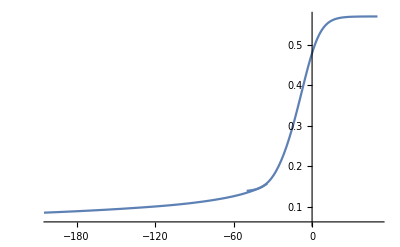

```mathematica
Show[Plot[2 phidot[t+tmatch-ti],{t,-(tmatch-ti),50}],Plot[ωBoB[t],{t,-50,50}],PlotRange->{{-200,50},All}]
```

```mathematica
LSFResidualω[t_] :=((2 phidot[t+tmatch-ti])^2-ωBoB[t]^2)^2
```

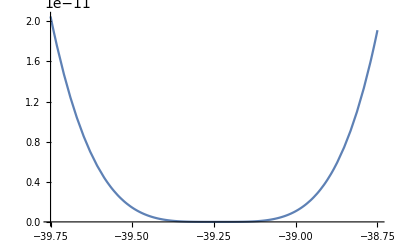

```mathematica
Plot[LSFResidualω[t] ,{t,-39.75,-38.75}]
```

```mathematica
tf =- (39.75+38.75)/2
```

-39.25

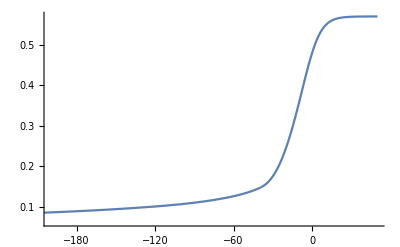

```mathematica
Show[Plot[2 phidot[t+tmatch-tf],{t,-(tmatch-tf),tf}],Plot[ωBoB[t],{t,tf,50}],PlotRange->{{-200,50},All}]
```

```mathematica
σf[t_]:=Piecewise[{{1,t>ti},{0,t<=ti}}];
Nσf[t_]:=Piecewise[{{1,t>tf },{0,t<=tf}}];
```

```mathematica
ωhyb[t_]:=(1-σf[t])2 phidot[t+tmatch-ti] +σf[t]ωBoB[t]
ωhybN[t_]:=(1-Nσf[t])2 phidot[t+tmatch-ti] +Nσf[t]ωBoB[t]
```

```mathematica
hre[tmatch]
```

{0.0119986}

```mathematica
AmpBoB[ti]/MaxAmpBoB
```

0.528802

```mathematica
NormRehins[t_]:=hre[t](AmpBoB[ti]/MaxAmpBoB)/Abs[hins[tmatch]];
```

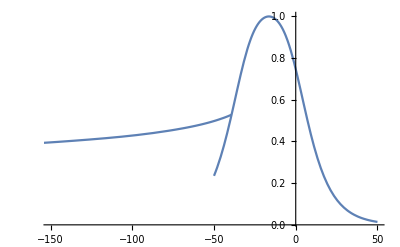

```mathematica
NormAmpins[t_]:=Abs[hins[t]]/Abs[hins[tmatch]]*AmpBoB[ti]/MaxAmpBoB
Show[Plot[AmpBoB[t]/MaxAmpBoB,{t,-50,50}],
Plot[NormAmpins[t+tmatch-ti],{t,-tmatch,ti}],PlotRange->{{-150,50},All}]
```

```mathematica
tAmp[t_]:=1/2(Abs[t-ti]/(t-ti)+1)
```

```mathematica
smooth[δ_,t_]:=Piecewise[{
{0,t<=ti-δ},
{1/((1+Exp[1/t-1/(1-t)])),ti-δ<t<ti+δ},
{1,True}}]
Plot[smooth[1/2,t],{t,ti-2,ti+2}]
```

```mathematica
LSFResidualA[t_] :=((AmpBoB[t]/MaxAmpBoB)-(NormAmpins[t+tmatch-ti]))^2
```

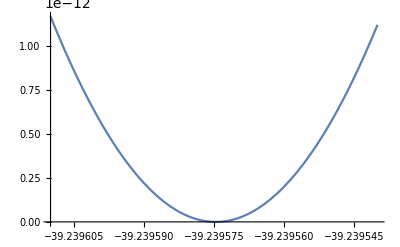

```mathematica
Plot[LSFResidualA[t] ,{t,-39.23961,-39.23954}]
```

```mathematica
tA=-(39.23961+39.23954)/2
```

-39.2396

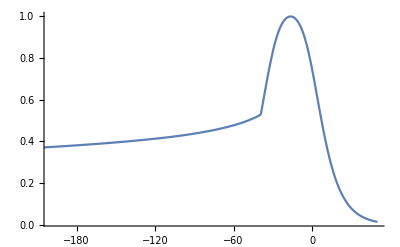

```mathematica
Show[Plot[NormAmpins[t+tmatch-ti],{t,-tmatch,tA}],Plot[AmpBoB[t]/MaxAmpBoB,{t,tA,50}],PlotRange->{{-200,50},All}]
```

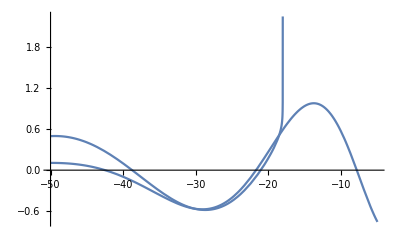

```mathematica
Show[Plot[NormRehins[t+tmatch-ti],{t,-50,-5}],Plot[-NormRehBoB[t+tfBoB],{t,-50,-5}],PlotRange->{{-50,-5},All}]
```

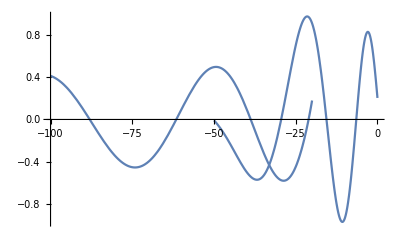

```mathematica
Show[Plot[NormRehins[t+tmatch-ti],{t,-100,-20}],Plot[-NormRehBoB[t],{t,-50,0}],PlotRange->{{-100,0},All}]
```

```mathematica
ti-tfBoB-0.5
```

-31.9974

```mathematica
ti-tfBoB
```

-31.4974

```mathematica
LSFResidualh[t_] :=((NormRehins[t+tmatch-ti])^2-(NormRehBoB[t+tfBoB])^2)^2
```

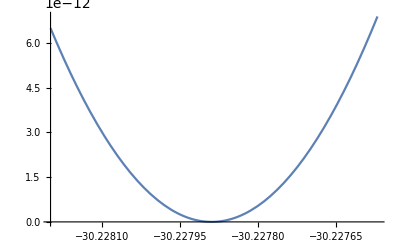

```mathematica
Plot[LSFResidualh[t] ,{t,-30.2282,-30.22757}]
```

```mathematica
th =- (30.2282+30.22757)/2
```

-30.2279

```mathematica
ti-tfBoB
```

-31.4974

```mathematica
δth=ti-tfBoB-th
```

-1.26947

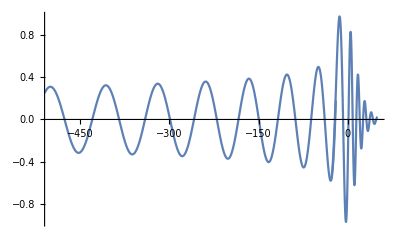

```mathematica
Show[Plot[NormRehins[t+tmatch-ti],{t,-tmatch,-20}],Plot[-NormRehBoB[t+tfBoB],{t,-30,50}],PlotRange->{{-500,50},All}]
```

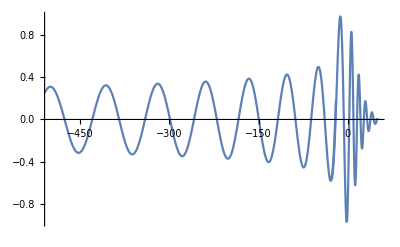

```mathematica
Show[Plot[NormRehins[t+tmatch-ti],{t,-tmatch,-20}],Plot[-NormRehBoB[t+tfBoB+δth],{t,-30,50}],PlotRange->{{-500,50},All}]
```

```mathematica
σh[t_]:=Piecewise[{{1,t>ti-tfBoB},{0,t<=ti-tfBoB}}];
Nσh[t_]:=Piecewise[{{1,t>th },{0,t<=th}}];
```

```mathematica
hhyb[t_]:=(1-σh[t])NormRehins[t+tmatch-ti] -σh[t]NormRehBoB[t+tfBoB]
```

```mathematica
hhybN[t_]:=(1-Nσh[t]) NormRehins[t+tmatch-ti] -Nσh[t] NormRehBoB[t+tfBoB]
```

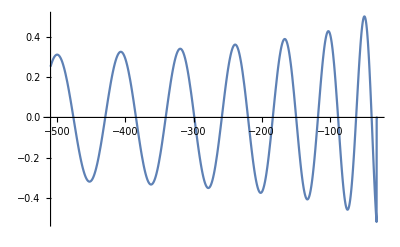

```mathematica
Plot[(1-σh[t])NormRehins[t+tmatch-ti],{t,-tmatch,th}]
```

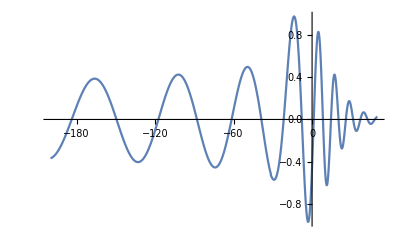

```mathematica
Plot[hhyb[t],{t,-200,50}]
```

```mathematica
Δphi = phi[tmatch] - Re[ϕBoB[tf]]
```

{21.1118}

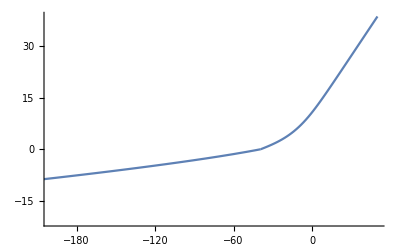

```mathematica
Show[Plot[phi[t+tmatch-tf]-Δphi,{t,-(tmatch-tf),tf}],Plot[ϕBoB[t],{t,tf,50}],PlotRange->{{-200,50},All}]
```

Plots for paper:

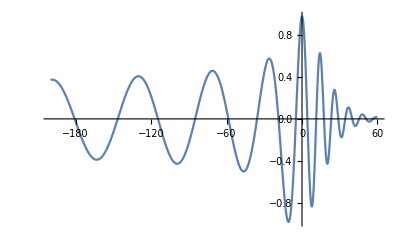

```mathematica
(*strain*)
Plot[-hhybN[t+δ],{t,-200,60}]
```

InterpolatingFunction::dmval: Input value {558.41} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {558.42} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

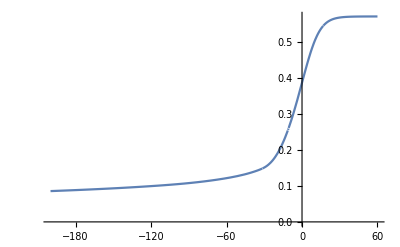

```mathematica
(*frequency*)
Plot[ωhybN[t+tfBoB],{t,-200,60}]
```

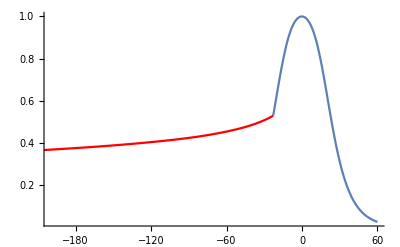

```mathematica
(*amplitude*)
Show[Plot[AmpBoB[t+t0BoB]/MaxAmpBoB,{t,tA-t0BoB,60}],Plot[NormAmpins[t+tmatch-ti+t0BoB],{t,-tmatch,tA-t0BoB},PlotStyle->Red],PlotRange->{{-200,60},All}]
```

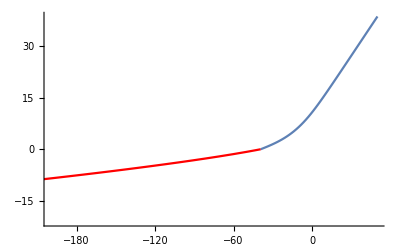

```mathematica
(*phase*)
Show[Plot[phi[t+tmatch-tf]-Δphi,{t,-(tmatch-tf),tf},PlotStyle->Red],Plot[ϕBoB[t],{t,tf,50}],PlotRange->{{-200,50},All}]
```

## Below are tables and exporting for plotting in Python

```mathematica
dt=0.1;
```

```mathematica
tArray5=Table[t,{t,-(tmatch-tf),tf,dt}];
```

```mathematica
phiPN=Table[phi[t+tmatch-tf]-Δphi,{t,-(tmatch-tf),tf,dt}];
```

```mathematica
phiPNvsTimeTab=Partition[Riffle[tArray5,phiPN],2];
```

```mathematica
PrependTo[phiPNvsTimeTab, {"t(M)", "ϕ(t)"}];
```

```mathematica
Export["dropbox/dillon/paperplottingwork/phiPN.txt",phiPNvsTimeTab]
```

dropbox/dillon/paperplottingwork/phiPN.txt

```mathematica
tArray6=Table[t,{t,tf,50,dt}];
```

```mathematica
phiBOB=Table[ϕBoB[t],{t,tf,50,dt}];
```

```mathematica
phiBOBvsTimeTab=Partition[Riffle[tArray6,phiBOB],2];
```

```mathematica
PrependTo[phiBOBvsTimeTab, {"t(M)", "ϕ(t)"}];
```

```mathematica
Export["dropbox/dillon/paperplottingwork/phiBOB.txt",phiBOBvsTimeTab]
```

dropbox/dillon/paperplottingwork/phiBOB.txt

```mathematica
(*tArray=Table[t,{t,-200,50,dt}];*)
```

```mathematica
(*hTab=Table[-hhybN[t+δ],{t,-200,50,dt}];*)
```

```mathematica
(*hvsTimeTab=Partition[Riffle[tArray,hTab],2];*)
```

```mathematica
(*PrependTo[hvsTimeTab, {"t(M)", "h(t)"}];*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/hMatched.txt",hvsTimeTab]*)
```

```mathematica
(*tArray1=Table[t,{t,-(tmatch-ti),ti,dt}];*)
```

```mathematica
(*wIRSTab=Table[2 phidot[t+tmatch-ti],{t,-(tmatch-ti),ti,dt}];*)
```

```mathematica
(*wIRSvsTimeTab=Partition[Riffle[tArray1,wIRSTab],2];*)
```

```mathematica
(*PrependTo[wIRSvsTimeTab, {"t(M)", "w(t)"}];*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/wIRS.txt",wIRSvsTimeTab]*)
```

```mathematica
(*tArray2=Table[t,{t,ti,50,dt}];*)
```

```mathematica
(*wBoBTab=Table[ωBoB[t],{t,ti,50,dt}];*)
```

```mathematica
(*wBoBvsTimeTab=Partition[Riffle[tArray2,wBoBTab],2];*)
```

```mathematica
(*PrependTo[wBoBvsTimeTab, {"t(M)", "w(t)"}];*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/wBoB.txt",wBoBvsTimeTab]*)
```

```mathematica
(*whybTab=Table[ωhybN[t],{t,-200,50,dt}];*)
```

```mathematica
(*whybvsTimeTab=Partition[Riffle[tArray,whybTab],2];*)
```

```mathematica
(*PrependTo[whybvsTimeTab, {"t(M)", "w(t)"}];*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/whyb.txt",whybvsTimeTab]*)
```

```mathematica
(*tArray3=Table[t,{t,tA-t0BoB,50,dt}];*)
```

```mathematica
(*AmpBoBTab=Table[AmpBoB[t+t0BoB]/MaxAmpBoB,{t,tA-t0BoB,50,dt}];*)
```

```mathematica
(*AmpBoBvsTimeTab=Partition[Riffle[tArray3,AmpBoBTab],2];*)
```

```mathematica
(*PrependTo[AmpBoBvsTimeTab, {"t(M)", "hAmp(t)"}];*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/hAmpBoB.txt",AmpBoBvsTimeTab]*)
```

```mathematica
(*tArray4=Table[t,{t,-tmatch,tA-t0BoB,dt}];*)
```

```mathematica
(*AmpIRSTab=Table[NormAmpins[t+tmatch-ti+t0BoB],{t,-tmatch,tA-t0BoB,dt}];*)
```

```mathematica
(*AmpIRSvsTimeTab=Partition[Riffle[tArray4,AmpIRSTab],2];*)
```

```mathematica
(*PrependTo[AmpIRSvsTimeTab, {"t(M)", "hAmp(t)"}];*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/hAmpIRS.txt",AmpIRSvsTimeTab]*)
```